# Funcs

```mathematica
SetDirectory[ NotebookDirectory[]];
<<"functions/Sensor.mx";
```

```mathematica
SSDegCalc[fn_] :=Module[{},
samples = 20000;
A = Import["data/"<>fn<>".csv"]/. n_?NumericQ/;n>0->1;
AnN = Dimensions[A]⟦2⟧;
PlN = Dimensions[A]⟦1⟧;An0=ConstantArray[0,{PlN,PlN}];
Pl0 =ConstantArray[0,{AnN,AnN}];
Asq= ArrayFlatten[{{An0,A},{Transpose@A,Pl0}}];
G = DirectedGraph[AdjacencyGraph[Asq],GraphLayout->"BipartiteEmbedding"];
SS = SScalc[G,samples];
VD =VertexDegree@AdjacencyGraph@Asq; 
Export["data/data_sensor/"<>fn<>"_SS.csv",SS];
Export["data/data_sensor/"<>fn<>"_VD.csv",VD];
 {SS,VD}
]
PlotTimeSeries[fn_ ,rt_,SS_]:=Module[{},
mt=Transpose[Import["data/data_sims/"<>fn<>"_mean_reps_"<>ToString[rt]<>".csv","Table"]];
m = Table[Append[mt⟦i⟧,0],{i,Length[mt]}];
If[SS=="Import",
SensorScore = Import["data/data_sensor/"<>fn<>"_SS.csv"]//Flatten,SensorScore=SS];
OrderS=Reverse[Ordering[SensorScore]];
c2=Reverse@Table[(Blend[{ RGBColor[0.8300000000000001, 0, 1],RGBColor[0, 0.85, 0.65]},Rescale[#,{0,1}]]&)[i],{i,0,1,1/(Length[m]-1)}];
TicksL =Table[{i,ToString[NumberForm[N[1-i/71],{3,1}]]},{i,Range[0,71,71/5]}];
ListPlot[m⟦OrderS⟧,
Joined->True,
Frame->True,
PlotStyle->Partition[c2,1],
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,191},
PlotRange->{Automatic,Automatic},
FrameTicksStyle->11,
FrameTicks->{{Range[0,100,20],None} ,{TicksL,None}},
FrameLabel->{"mutualistic strength","mean abundance"}
]
]
```

```mathematica
ImportEWS[fn_,mR_,MR_] := Module[{}, Table[Import["data/data_EWS/"<>fn<>"EWS"<>ToString[i]<>".csv","Table"]//Flatten,{i,mR,MR}]]

colors={RGBColor[0.863, 0.133, 0.196],RGBColor[0.17600000000000002, 0.41600000000000004, 0.631],RGBColor[0.9690000000000001, 0.6859999999999999, 0.20800000000000002],RGBColor[0.349, Rational[7, 10], 0.33299999999999996],RGBColor[1, 0.5, 0],RGBColor[0.557, 0.573, 0.569]};
GetColor[deg_]:=Module[{},
Which[
deg ==1, colors⟦1⟧,
deg==2,colors⟦2⟧,
deg==3, colors⟦3⟧,
True, colors⟦6⟧
]];
GetLab[deg_]:=Module[{},
Which[
deg ==1,"degree = 1",
deg==2,"degree = 2",
deg==3, "degree = 3",
deg == 4, "degree > 3"
]];
SsEwsTemps[fn_,rt_,minR_,maxR_,VD_,SS_]:=Module[{},
EWSall=ImportEWS[fn,minR,maxR];
If[rt=="Median",
thisEW = Median@EWSall//Flatten,
thisEW = EWSall⟦rt⟧//Flatten];
If[VD=="Import",
VertexDeg = Import["data/data_sensor/"<>fn<>"_VD.csv"]//Flatten,
VertexDeg=VD];
If[SS=="Import",
SensorScore = Import["data/data_sensor/"<>fn<>"_SS.csv"]//Flatten,SensorScore=SS];
n = Length@SensorScore;
degrees = Sort@DeleteDuplicates@VertexDeg;
temp=Table[
pos = Position[VertexDeg,deg]//Flatten;
ListPlot[Thread[{thisEW⟦pos⟧, SensorScore⟦pos⟧}],
PlotRange->{{0-0.01,Max@thisEW+0.01},{-0.05,1}},
(*GridLines->{{},{Max@SensorScore}},
GridLinesStyle->Directive[Gray,Dashed],*)
PlotStyle->Directive[GetColor[deg], PointSize[0.03],Opacity[0.7]],
 FrameTicks->{{Range[0,1,0.2],None},{Range[0,Max@thisEW,0.05],None}},
ScalingFunctions->{"Reverse",Identity},
Frame->True
]
,{deg,degrees}];
temp2 = ListPlot[Thread[{thisEW, SensorScore}],
PlotRange->{{0-0.01,Max@thisEW+0.01},{-0.05,1}},
(*GridLines->{{},{Mean@SensorScore}},
GridLinesStyle->Directive[Gray,Dashed],*)
FrameTicks->{{Range[0,1,0.2],None},{Range[0,Max@thisEW,0.05],None}},
ScalingFunctions->{"Reverse",Identity},
Frame->True,
PlotStyle-> Directive[Black, PointSize[0.04],Opacity[1]],
FrameLabel->{"early-warning score","sensor score"}
];
temp3 = ListPlot[Thread[{thisEW, SensorScore}],
ScalingFunctions->{"Reverse",Identity},
PlotStyle-> Directive[White, PointSize[0.03],Opacity[1]]
];
Leg = Show[Table[ListPlot[{-i},
PlotStyle->Directive[GetColor[i], PointSize[0.03],Opacity[1]],
PlotLegends->{GetLab[i]}],{i,4}]];
{temp2,temp3,temp,Leg}
]

PlotEWscoreSensorScore[fn_,rt_,minR_,maxR_,VertexDeg_,SensorScore_]:=Module[{},
{t1, t2, t3,Leg} = SsEwsTemps[fn,rt,minR,maxR,VertexDeg,SensorScore];
Show[t1,t2,t3,Leg,
ImageSize->{Automatic,198},
FrameTicksStyle->12
]
]
```

```mathematica
PlotEWscoreRatio[fn_,minR_,maxR_,VD_,SS_]:=Module[{},
numberofsamples=300;
EWnom=ImportEWS[fn,minR,maxR];
If[VD=="Import",
vertexDegree= Import["data/data_sensor/"<>fn<>"_VD.csv"]//Flatten,
vertexDegree=VD];
If[SS =="Import",
SensorScore = Import["data/data_sensor/"<>fn<>"_SS.csv"]//Flatten,SensorScore=SS];
n = Length@SensorScore;
ϵ=0.01;
(* order by sensor score *)
ewratio=
Flatten[
ParallelTable[
order = Reverse@Ordering[SensorScore+RandomReal[{-ϵ,ϵ}, Length@SensorScore]];
Table[
Table[
Max@Take[EWnom⟦i⟧⟦order⟧,size]/Max@EWnom⟦i⟧
,{size, 1,Length@EWnom⟦i⟧}]
,{i,1,Length@EWnom}]
,{samples, numberofsamples}],1];
(* order by degree *)
ewratioD=
Flatten[
ParallelTable[
orderD = Ordering[vertexDegree+RandomReal[{-0.3,0.3}, Length@vertexDegree]];
Table[
Table[
Max@Take[EWnom⟦i⟧⟦orderD⟧,size]/Max@EWnom⟦i⟧
,{size, 1,Length@EWnom⟦i⟧}]
,{i,1,Length@EWnom}]
,{k,1,numberofsamples}],1];
(* random order *)
ewratioRand=
Flatten[
ParallelTable[
orderD = RandomSample[Range@Length@EWnom⟦1⟧, Length@EWnom⟦1⟧];
Table[
Table[
Max@Take[EWnom⟦i⟧⟦orderD⟧,size]/Max@EWnom⟦i⟧
,{size, 1,Length@EWnom⟦i⟧}]
,{i,1,Length@EWnom}]
,{k,1,numberofsamples}],1];
Show[
ListPlot[Thread[{(1/n)Range@n,Median@ewratioD}], 
Joined->True, 
InterpolationOrder->0, 
PlotRange->{{Automatic,0.8},{0,1.05}},
Frame -> True,
FrameTicks->{{Range[0,1,0.2],None},{Range[0,1,0.2],None}},
FrameTicksStyle->11,
PlotLegends-> {"by degree"},
(*GridLines->{{{MSSsize⟦network⟧/n, Dashed},Count[vertexDegree,1]/n},{}},*)
PlotRange->{Automatic,{0,1}},
PlotStyle->Directive[RGBColor[1, 0, 0.67],Opacity[1],  Thickness[0.008]],
FrameLabel->{"fraction of measured species","early-warning score ratio"}
]
,
ListPlot[{
Thread[{(1/n)Range@n,Quantile[ewratioD,1/4]}],
Thread[{(1/n)Range@n,Quantile[ewratioD,3/4]}]
},
Joined->True,
PlotStyle->Directive[RGBColor[1, 0, 0.67],Opacity[1], Thickness[0.001]],
Filling->{1->{2}},
FillingStyle->Directive[RGBColor[1, 0, 0.67],Opacity[0.05]],
InterpolationOrder->0
]
,
ListPlot[Thread[{(1/n)Range@n,Median@ewratioRand}], 
Joined->True, 
InterpolationOrder->0, 
PlotRange->All,
Frame -> True,
GridLines->{{{1/n, Dashed},Count[vertexDegree,1]/n},{}},
PlotRange->{Automatic,{0,1}},
PlotStyle->Directive[Gray,Opacity[1], Thick],
PlotLegends-> {"at random"}
]
,
ListPlot[{
Thread[{(1/n)Range@n,Quantile[ewratioRand,1/4]}],
Thread[{(1/n)Range@n,Quantile[ewratioRand,3/4]}]
},
Joined->True,
PlotStyle->Directive[Gray,Opacity[1], Thickness[0.001]],
Filling->{1->{2}},
FillingStyle->Directive[Gray,Opacity[0.05]],
InterpolationOrder->0
]
,
ListPlot[Thread[{(1/n)Range@n,Median@ewratio}], 
Joined->True, 
InterpolationOrder->0, 
Frame -> True,
GridLines->{{{1/n, Dashed},Count[vertexDegree,1]/n},{}},
PlotRange->{Automatic,{0,1}},
PlotStyle->Directive[RGBColor[0, 0.75, 0.65],Opacity[1], Thickness[0.01]],
PlotLegends-> {"by sensor score"}
]
,
ListPlot[{
Thread[{(1/n)Range@n,Quantile[ewratio,1/4]}],
Thread[{(1/n)Range@n,Quantile[ewratio,3/4]}]
},
Joined->True,
PlotRange->All,
PlotStyle->Directive[RGBColor[0, 0.75, 0.65],Opacity[1], Thickness[0.002]],
Filling->{1->{2}},
FillingStyle->Directive[RGBColor[0, 0.75, 0.65],Opacity[0.1]],
InterpolationOrder->0
]
, 
ImageSize->{Automatic,191},
FrameTicksStyle->12
]
]
```

```mathematica
PlotEWscoreRatioHistogram[fn_,minR_,maxR_,VD_,SS_]:=Module[{},
numberofsamples=300;
EWnom=ImportEWS[fn,minR,maxR];
If[VD=="Import",
vertexDegree= Import["data/data_sensor/"<>fn<>"_VD.csv"]//Flatten,
vertexDegree=VD];
If[SS =="Import",
SensorScore = Import["data/data_sensor/"<>fn<>"_SS.csv"]//Flatten,SensorScore=SS];
n = Length@SensorScore;
ϵ=0.01;
dataS=
Table[
ParallelTable[
orderS = Reverse@Ordering[SensorScore+RandomReal[{-ϵ,ϵ}, Length@SensorScore]]; (* by sensor*)
orderR = RandomSample[Range@Length@EWnom⟦1⟧, Length@EWnom⟦1⟧];   (* at random*)
Max@Take[EWnom⟦i⟧⟦orderS⟧,1]/Max@EWnom⟦i⟧-Max@Take[EWnom⟦i⟧⟦orderR⟧,1]/Max@EWnom⟦i⟧
(*Max@Take[EWnom⟦i⟧⟦orderR⟧,1]/Max@EWnom⟦i⟧*)
,{k,1,numberofsamples}]
,{i,1,Length@EWnom}]//Flatten;
dataD=
Table[
ParallelTable[
orderD = Ordering[vertexDegree+RandomReal[{-0.3,0.3}, Length@vertexDegree]]; (* by degree*)
orderR = RandomSample[Range@Length@EWnom⟦1⟧, Length@EWnom⟦1⟧];   (* at random*)
Max@Take[EWnom⟦i⟧⟦orderD⟧,1]/Max@EWnom⟦i⟧-Max@Take[EWnom⟦i⟧⟦orderR⟧,1]/Max@EWnom⟦i⟧
(*Max@Take[EWnom⟦i⟧⟦orderD⟧,1]/Max@EWnom⟦i⟧*)
,{k,1,numberofsamples}]
,{i,1,Length@EWnom}]//Flatten;
{Show[
DistributionChart[{dataS, dataD},
(*ChartElementFunction->"HistogramDensity",*)
Frame->{False, True, False, False},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,None}},
ImageSize->{Automatic,183},
GridLines->{{},{0}},
FrameTicksStyle->11,
ChartStyle->{{EdgeForm[None],EdgeForm[None]},{RGBColor[0, 0.75, 0.65],RGBColor[1, 0, 0.67]}},
ChartLegends->{"by sensor score", "by degree"},
AspectRatio->GoldenRatio
]
,
ListPlot[{Median@dataS,Median@dataD}, PlotStyle->Directive[Black, PointSize[0.06]]]
,
ListPlot[{
{1.007,Quantile[dataS,1/4]},
{1.007,Quantile[dataS,3/4]}
},Joined->True,PlotStyle->Directive[Black]]
,
ListPlot[{
{2.007,Quantile[dataD,1/4]},
{2.007,Quantile[dataD,3/4]}
},Joined->True,PlotStyle->Directive[Black]]
], {"median by sensor: "<> ToString@Round[Median@dataS,.0001]}, {"median by degree: "<>ToString@Round[Median@dataD,.0001]}}//TableForm
]
```

```mathematica
RunEWAnalysis[fn_,rep_,minReps_,maxReps_]:=Module[{},
SSt =  "Import";
VDt = "Import";
TS =PlotTimeSeries[fn,rep,SSt];
EWSSSt = PlotEWscoreSensorScore[fn,rep,minReps,maxReps,SSt,VDt];
EWSSSmed = PlotEWscoreSensorScore[fn,"Median",minReps,maxReps, SSt,VDt];
EWSR = PlotEWscoreRatio[fn,minReps,maxReps, SSt,VDt];
EWSRH = PlotEWscoreRatioHistogram[fn,minReps,maxReps,SSt,VDt];
{
{""},
{"Realization: "<>ToString[rep]<> ", Network: "<>fn},
{""},
{TS,EWSSSt},
{""},
{""},
{"All realizations, Network: "<>fn},
{""},
{EWSSSmed,
EWSR,
EWSRH}
}//TableForm
]
```

# Main

## Mount Missim

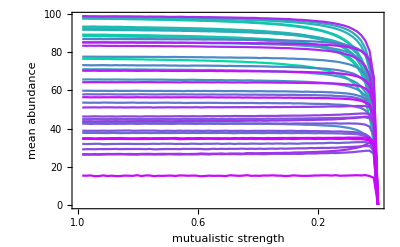
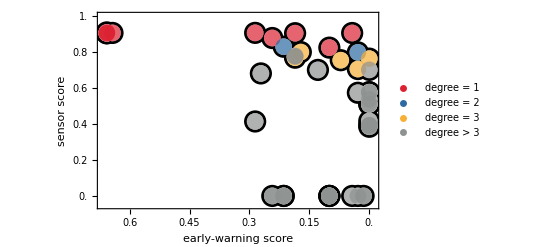
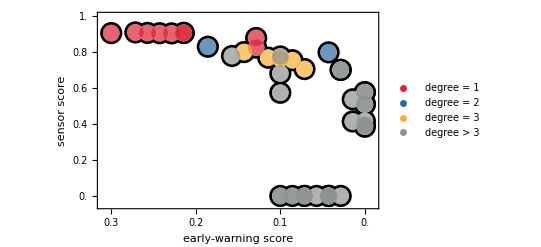
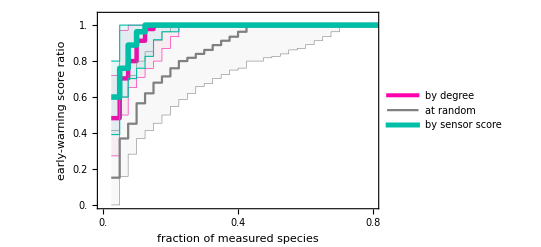
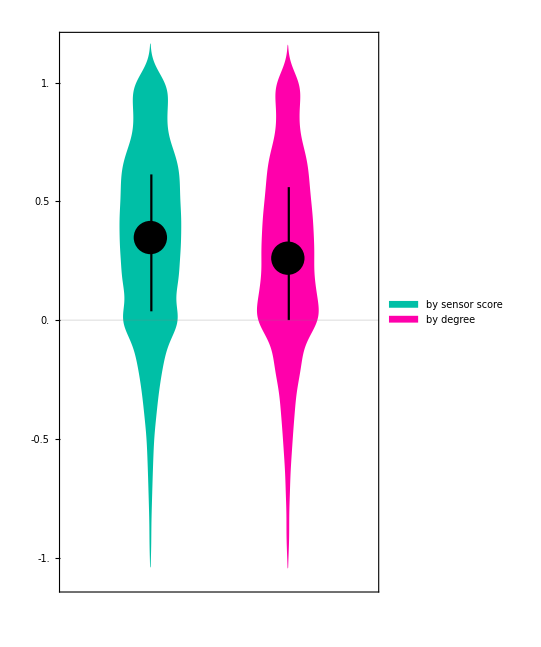
|  | 
Realization: 6, Network: M_SD_002 |  | 
 |  | 
-Graphics- | -Graphics- | 
 |  | 
 |  | 
All realizations, Network: M_SD_002 |  | 
 |  | 
-Graphics- | -Graphics- | -Graphics-
median by sensor: 0.3478
median by degree: 0.2609

```mathematica
fn = "M_SD_002";  (*Enter the network matrix csv filename here. The matrix must be rectangular and have plants as rows and animals as columns*)
kStart=0; (*Enter the initial realization (default =0)*)
kEnd=18; (*Enter the total number of realizations*)
kT=6; (*choose one particular realization to display*)

 (* If Sensor Score and Vertex Degree have been calculated before and saved in "data/data_sensor/",  as "fn_SS.scv" and "fn_VD.csv", respectively, comment the following line to avoid re-calculating them and overwriting the files*)
(*{SensorScoret,VertexDegt}=SSDegCalc[fn,True];*)

(* main function *)
RunEWAnalysis[fn,kT,kStart,kEnd]
```

## Genebra

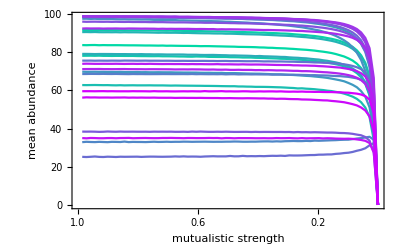
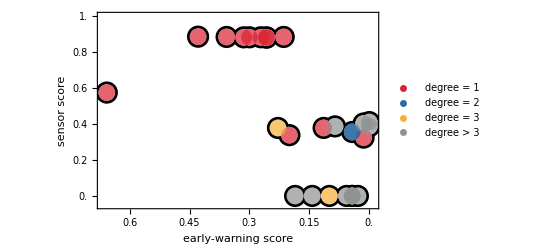
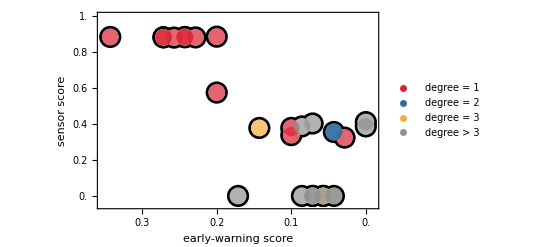
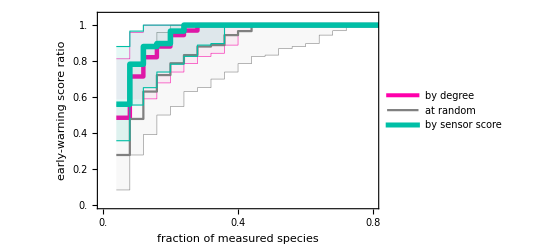
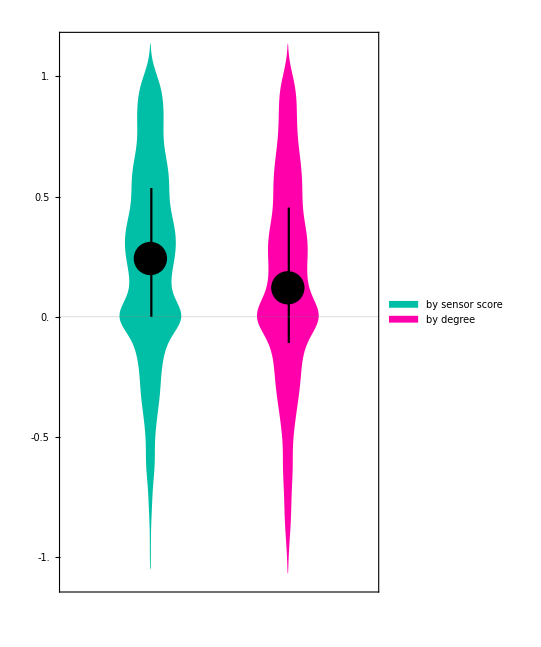
|  | 
Realization: 4, Network: M_SD_009 |  | 
 |  | 
-Graphics- | -Graphics- | 
 |  | 
 |  | 
All realizations, Network: M_SD_009 |  | 
 |  | 
-Graphics- | -Graphics- | -Graphics-
median by sensor: 0.2424
median by degree: 0.1206

```mathematica
fn = "M_SD_009";  (*Enter the network matrix csv filename here. The matrix must be rectangular and have plants as rows and animals as columns*)
kStart=0; (*Enter the initial realization (default =0)*)
kEnd=18; (*Enter the total number of realizations*)
kT=4; (*choose one particular realization to display*)

 (* If Sensor Score and Vertex Degree have been calculated before and saved in "data/data_sensor/",  as "fn_SS.scv" and "fn_VD.csv", respectively, comment the following line to avoid re-calculating them and overwriting the files*)
{SensorScoret,VertexDegt}=SSDegCalc[fn,True];

(* main function *)
RunEWAnalysis[fn,kT,kStart,kEnd]
```

## Calton

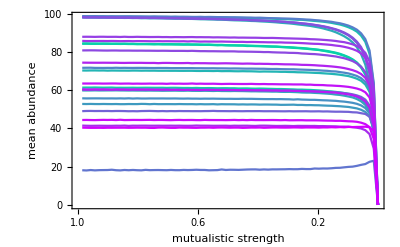
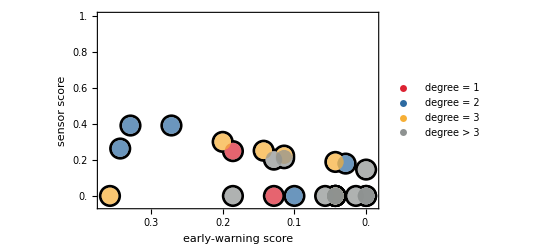
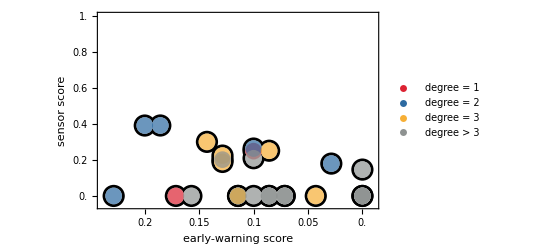
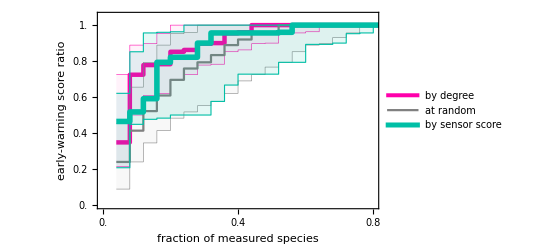
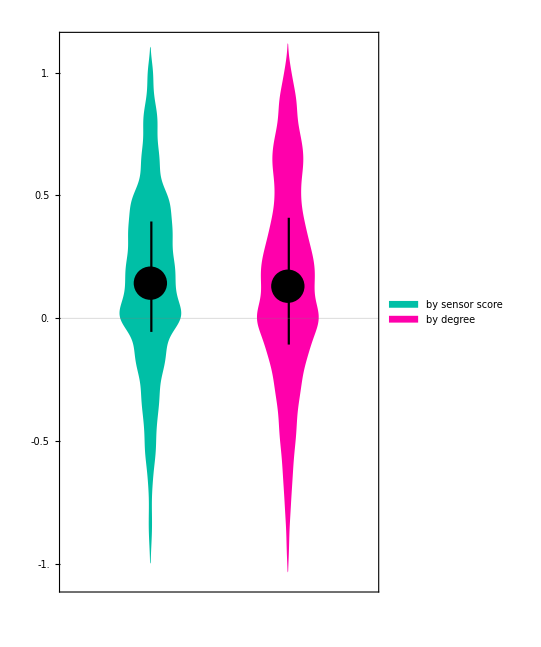
|  | 
Realization: 7, Network: M_SD_011 |  | 
 |  | 
-Graphics- | -Graphics- | 
 |  | 
 |  | 
All realizations, Network: M_SD_011 |  | 
 |  | 
-Graphics- | -Graphics- | -Graphics-
median by sensor: 0.1429
median by degree: 0.1304

```mathematica
fn = "M_SD_011";  (*Enter the network matrix csv filename here. The matrix must be rectangular and have plants as rows and animals as columns*)
kStart=0; (*Enter the initial realization (default =0)*)
kEnd=18; (*Enter the total number of realizations*)
kT=7; (*choose one particular realization to display*)

 (* If Sensor Score and Vertex Degree have been calculated before and saved in "data/data_sensor/",  as "fn_SS.scv" and "fn_VD.csv", respectively, comment the following line to avoid re-calculating them and overwriting the files*)
{SensorScoret,VertexDegt}=SSDegCalc[fn,True];

(* main function *)
RunEWAnalysis[fn,kT,kStart,kEnd]
```